```mathematica
applyForces=Function[{node,force,timeStep},
node+force*timeStep
];

calcPairwiseForce=Function[{node1,node2},Module[{distance,intendedDistance,displacement,force},
distance=EuclideanDistance[node1,node2];
intendedDistance=1;
displacement=node2-node1;
force=(1-intendedDistance/distance)*displacement*0.3
]
];

calcAndApply=Function[timeStep,
Function[t,Module[{l,forces,newNodes,i,j,resultingForce},
l=Length[nodes];
forces=Table[{0,0},l];
newNodes=Table[Null,l];
i=1;
While[i≤l,
j=i+1;
While[j≤l,
resultingForce=calcPairwiseForce[nodes[[i]],nodes[[j]]];
forces[[i]]=forces[[i]]+resultingForce;
forces[[j]]=forces[[j]]-resultingForce;
j++
];
newNodes[[i]]=applyForces[nodes[[i]],forces[[i]],timeStep];
i++
];
nodes=newNodes
]
]
];
```

```mathematica
Animate[Graph[{1<->2,2<->3,3<->1,3<->4,4<->5,5<->6,6<->1},VertexCoordinates->update[t],Frame->True,PlotRange->{{-4,8},{-16,0}},GridLines->Automatic],{t,0,tMax,timeStep}]
```

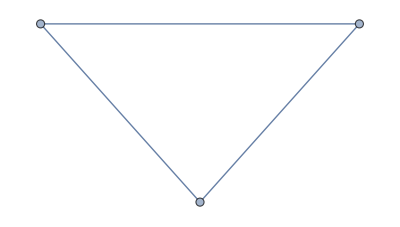

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexCoordinates->update[]]
```

```mathematica
Manipulate[x,{x,0,1}]
```

```mathematica
DynamicModule[{col=Green},EventHandler[Style["text",FontColor->Dynamic[col]],{{"KeyDown","ShiftKey"}:>Print[ok]}
]
]
```

```mathematica
x
```

```mathematica
x
```

```mathematica
⌘
```

⌘

```mathematica
DynamicModule[{key="x"},EventHandler[Print[Dynamic[key]],{"KeyDown":>(key=CurrentValue["EventKey"])}]];
```

```mathematica
event
```

```mathematica
s
```

```mathematica
DynamicModule[{col=Green},EventHandler[Style[Dynamic@key,FontColor->Dynamic[col]],{"KeyDown":>(key=CurrentValue["EventKey"])}
]
]
```

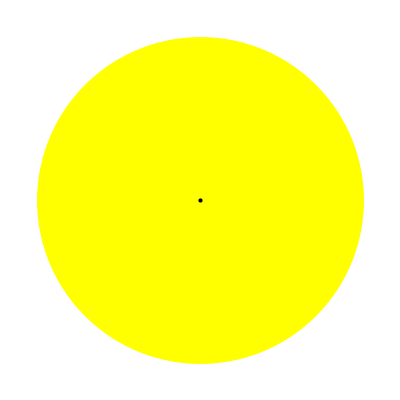

yes

yes

yes

«2 more identical outputs»

```mathematica
EventHandler[
ClickPane[Graphics[{Yellow,Disk[pt],Black,Point[pt]},ImageSize->Tiny],(pt=#)&],{"MouseClicked":>Print[yes]}
]
```

```mathematica
EventHandler[
Pane[Graphics[{Yellow,Disk[{0,0}],Black,Point[{0,0}]},ImageSize->Tiny],ImageSize->Large],{"MouseClicked":>Print[yes]}
]
```

-Graphics-

yes

yes

yes

```mathematica
update=calcAndApply[timeStep];
nodes=Table[{i,-(i-2)^2},{i,1,6}]
timeStep=0.1;
tMax=10;
```

{{1,-1},{2,0},{3,-1},{4,-4},{5,-9},{6,-16}}

```mathematica
graphStructure={{1},{},{{0,0}}};
EventHandler[
Dynamic@GraphPlot[Graph[graphStructure[[1]],graphStructure[[2]], VertexCoordinates->graphStructure[[3]]],VertexSize->{2,2},Frame->True,PlotRange->100,FrameTicks->Automatic,GridLines->Automatic],
{"MouseClicked":>(mouseClicked=True, mousePosition=MousePosition[])},
{{"KeyDown","n"}:>(newNode=True)},
{{"KeyDown","e"}:>(newEdge=True)},
{{"KeyDown","z"}:>(newEdge=True)}

]
```

```mathematica
notNull=Function[x,
Not[TrueQ[x==Null]]
];

graphPanel=Function[
Module[
{
aMatrix=Table[0,{i,2},{j,2}],
nodeCoords={{0,0},{15,15}},
originNode=Null,
invisibleEdge={Opacity[0],Arrow[{{0,0},{0,0}}]},
tempEdge,
locked=False,
arrivalNode=Null
},

tempEdge=invisibleEdge;

resetActionVariables=Function[
tempEdge=invisibleEdge;
originNode=Null;
arrivalNode=Null;
locked=False;
];

addNode=Function[
Block[
{
numberOfNodes,newAMatrix,i
},
numberOfNodes=Length[aMatrix];
newAMatrix=aMatrix;
AppendTo[newAMatrix,Table[0,{j,numberOfNodes}]];
i=1;
While[i≤numberOfNodes+1,
AppendTo[newAMatrix[[i]],0];
i++;
];
AppendTo[nodeCoords,MousePosition["Graphics"]];
aMatrix=newAMatrix;
]
];

addEdge=Function[
aMatrix[[originNode,arrivalNode]]=1
];

drawArrow=Function[
Block[
{
displacement,
displacementNorm,
offset
},
If[notNull[originNode],
arrivalNode=getClosestNode[];

If[notNull[arrivalNode]&&arrivalNode≠originNode,
locked=True;
tempEdge={Opacity[1],Arrowheads[0.03],Arrow[{nodeCoords[[originNode]],nodeCoords[[arrivalNode]]},2]},

locked=False;
displacement=MousePosition["Graphics"]-nodeCoords[[originNode]];
displacementNorm=Norm[displacement];
If[displacementNorm>3,
offset=displacement*2/displacementNorm;
tempEdge={Opacity[1],Arrowheads[0.03],Arrow[{nodeCoords[[originNode]]+offset,MousePosition["Graphics"]}]}
]
]
]
]
];


getClosestNode=Function[
Block[
{
n,singleValue,distance,closestNode,i,newDistance
},
n=Length[nodeCoords];
singleValue=True;
distance=Infinity;
closestNode=Null;
i=1;
While[i≤n&&singleValue,
newDistance=EuclideanDistance[nodeCoords[[i]],MousePosition["Graphics"]];
If[newDistance==distance,
singleValue=False,
If[(newDistance<distance)&&(newDistance<4),
distance=newDistance;
closestNode=i
]
];
i++
];
closestNode
]
];


handleAction=Function[event,
Block[{modKey,l},
modKey=CurrentValue["ModifierKeys"];
l=Length[modKey];
Which[
l==0&&event=="MouseClicked",addNode[],
l==0&&event=="MouseDown",originNode=getClosestNode[],
l==0&&event=="MouseDragged",drawArrow[],
event=="MouseUp"&&Not[locked],resetActionVariables[],
event=="MouseUp"&&locked,addEdge[];resetActionVariables[]

]
]
];


EventHandler[
Dynamic@AdjacencyGraph[aMatrix,VertexCoordinates->nodeCoords,Epilog->tempEdge,VertexSize->{2,2},Frame->True,PlotRange->30,FrameTicks->Automatic,GridLines->Automatic],
{
"MouseDragged":>(handleAction["MouseDragged"]),
"MouseClicked":>(handleAction["MouseClicked"]),
"MouseDown":>(handleAction["MouseDown"]),
"MouseUp":>(handleAction["MouseUp"])
}
]
]
];
```

```mathematica
graphPanel[]
```

```mathematica
modKey=={"Command","Alt"}
```